Autocorrelations for Generalised Hybrid Monte Carlo

## Quadratic Operators with Exponentially Distributed Trajectories

Based on the paper, “Cost of the Generalised Hybrid Monte Carlo Algorithm for Free Field Theory”, this notebook contains a Mathematica format for selected equations. The aim is to provide a dynamic method of working with the theory.

The paper provides the Laplace Transform of the autocorrelations which will be denoted by F[...] where β is the Laplace transformed time, t

Unless explicitly stated, all equations are in Laplace Transformed format

Throughout the plots, the following parameters will be used:

```mathematica
Clear[τ,r,ϕ,θ,ρ, tf, steps, dtau, traj, rate, j , k, μ, ν];
Clear[ F, rawF, Funit, FHMC, FHMCunit];
Clear[iF, iFunit,iFHMC, iFHMCunit,iFHMC, iFHMCunit];
Clear[A, Aunit, AHMC, AHMCunit];
Clear[CF, CFunit, CHMC, CHMCunit];
Clear[Cunit, Cunitn];
Clear[CFn, CFunitn, CHMCn, CHMCunitn];
Clear[B, g, gp, gm, gp20, gm00, gp11, gp02];
Clear[gn0, gn1, gn2, gn3, gd0, gd1, gd2, gd3];
Clear[fG, fGHMC]; 
Clear[tmp0, tmp1, tmp2, hmcTmp2, hmcTmp];
Clear[a0, a1, a2, a3, a4, a5, a6, a7, a8, a9];
tf = 50;
steps = 20;
dtau = 0.1;
traj = steps*dtau;
rate = 1/traj;
```

## Derivation of Laplace Transformed GHMC Autocorrelation Function

The following functions G^+ (gp) and G^- (gm) are defined for the exponentially distributed trajectories as,

```mathematica
B[k_] := If[IntegerQ[k/2],β τ+1,(j+k-2 μ - 2 ν)ϕ];
g [j_,k_]:=Sum[Sum[Binomial[j,μ]  Binomial[k,ν]((1/2)^(j+k)(-1)^(ν+(1/2 k))B[k])/((β τ+1)^2+ϕ^2(j+k-2μ-2ν)^2), {ν, 0, k}],{μ, 0, j}];
gp[j_, k_] := ρ  g[ j,k];
gm[j_, k_] := (1-ρ)g[j,k];
```

and are used to populate the following equations to obtain the Laplace Tranformed autocorrelation functions. 
The general case is given by populating,

```mathematica
gp20:= gp[2,0];
gm00 := gm[0,0];
gp11 := gp[1,1];
gp02 := gp[0,2];
```

```mathematica
gn0:=gp20+gm00;
gn1:=-gp20^2-2 gp11^2+gp02 gm00+gp02 gp20+gm00^2;
gn2:=-(gp20-gp02+gm00) (gm00+gp20+gp02);
gn3:=(gm00+gp20+gp02) (gp20^2-2 gp02 gp20+gp02^2+4 gp11^2-gm00^2);
gd0:=1-gm00-gp20;
gd1:=-(gp02 gm00-2 gp11^2+gm00^2+gp20 gp02-gm00+gp20-gp20^2-gp02);
gd2:=-(-gp20^2+gm00-2 gp20 gm00+gp02^2-gm00^2+gp20);
gd3:=2 gp11^2-gp02^3-4 gp11^2 gm00+gp02 gp20^2-gp02 gp20+gp02^2 gp20-gp02 gm00+gp20 gm00^2-gp20^3+gp20^2-gm00^2-4 gp20 gp11^2-gp20^2 gm00-4 gp11^2 gp02+gp02 gm00^2-gp02^2 gm00+gm00^3+2 gp02 gp20 gm00;
```

so the full form can be obtained by populating,

```mathematica
fG[β_, ϕ_, θ_,ρ_, τ_]:=(gn0+gn0 Cos[θ] + gn2 Cos[θ]^2+gn3 Cos[θ]^3)/(gd0+gd1 Cos[θ]+gd2 Cos[θ]^2+ gd3 Cos[θ]^3)
```

## HMC Condition

The HMC case is given by,

```mathematica
fGHMC[β_, ϕ_,ρ_, τ_] :=(gp20 + gm00)/(1-gp20 - gm00)
```

```mathematica
tmp1 := FullSimplify[fGHMC[β, ϕ,ρ, τ]];
hmcTmp[β_, ϕ_,ρ_, τ_] := Evaluate[Collect[Numerator[tmp1], β]/Collect[Denominator[tmp1],β]]
```

Checking the against the general case above,

```mathematica
FullSimplify[fGHMC[β, ϕ,ρ, τ] == fG[β, ϕ,π/2,ρ, τ]]
```

True

## Laplace Transformed GHMC Autocorrelation Function

The form is exceedingly long and so has been broken apart into testable segments specified by an[...],

```mathematica
a0[θ_,ρ_]:=-Cos[θ]^2+(1-2ρ)Cos[θ]+4
a1[θ_,ρ_] :=(-1+2ρ)Cos[θ]^3-3 Cos[θ]^2+(3-6ρ)Cos[θ]+6
a2[θ_,ρ_, ϕ_] :=(4ρ-2)Cos[θ]^3+((-2+2ρ)(ρ-2)ϕ^2+3-6ρ)Cos[θ] + ((4ρ-4)ϕ^2-3)Cos[θ]^2+(8-4ρ)ϕ^2+4
a3[θ_,ρ_, ϕ_] :=(4ρ-2)Cos[θ]^3+((4-4ρ)ϕ^2+3-6ρ)Cos[θ] + ((2ρ-4)ϕ^2-3)Cos[θ]^2+(8+2ρ)ϕ^2+4
a4[θ_,ρ_, ϕ_] :=(-4(-1+ρ)^2 ϕ^2-1+2ρ)Cos[θ]^3+((4ρ-4)ϕ^2-1)Cos[θ]^2+((-2+2ρ)(ρ-2)ϕ^2+1 -2ρ)Cos[θ] + (4-2ρ)ϕ^2+1
a5[θ_,ρ_, ϕ_] :=((2-2ρ)(ρ-2)ϕ^2-1+2ρ)Cos[θ]^3+(-4 ϕ^2-1)Cos[θ]^2+((-2ρ-4)(-1+ρ)ϕ^2+1-2ρ)Cos[θ]+(4ρ+4)ϕ^2+1
a6[θ_,ρ_, ϕ_] :=2ρ(-1+ρ)ϕ^2 Cos[θ]^3-2 Cos[θ]^2 ρ ϕ^2 - 2ρ(-1 + ρ)ϕ^2 Cos[θ]+2ρ ϕ^2
```

The Laplace Transform of the autocorrelation for quadratic operators is given by,

```mathematica
F[β_, ϕ_, θ_, ρ_, r_]:=(r β^4+a0[θ,ρ] r^2 β^3+(a1[θ,ρ]+(4-2ρ)ϕ^2)r^3 β^2 +a2[θ,ρ, ϕ] r^4 β+a4[θ,ρ, ϕ] r^5)/(β^5+a0[θ,ρ]r β^4+ (a1[θ,ρ]+4 ϕ^2)r^2 β^3 +a3[θ,ρ, ϕ] r^3 β^2+ a5[θ,ρ, ϕ] r^4 β + a6[θ,ρ, ϕ] r^5)
```

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
a7[θ_]:=-Cos[θ]+2-Cos[θ]^2
a8[θ_]:=Cos[θ]^3-Cos[θ]^2-Cos[θ]+1
```

```mathematica
Funit[β_, ϕ_, θ_, r_]:=(β^2 r+ β r^2 a7[θ] +r^3(Cos[θ]^3-Cos[θ]^2-Cos[θ]+2 ϕ^2+1))/(β^3+β^2 r a7[θ]+β r^2(a8[θ]+4 ϕ^2)+r^3(-2 Cos[θ]^2 ϕ^2+2 ϕ^2))
```

Check This should be equal to Equation (1) for ρ =1:

```mathematica
FullSimplify[Funit[β, ϕ, θ, r]==F[β, ϕ, θ, 1, r]]
```

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMC[β_,ϕ_, ρ_, r_]:= (β^2 r+ 2 r^2 β +  ϕ^2(4-2ρ)r^3 +r^3)/(β^3+2r β^2+(4 ϕ^2+1)r^2 β+2 r^3 ϕ^2 ρ)
```

Check This should be equal to Equation (1) for θ = π/2:

```mathematica
FullSimplify[F[β, 0, π/2, 0, 1]==FHMC[β,0,0, 1]]
```

True

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMCunit[β_, ϕ_, r_] :=(β^2 r+ 2β r^2 +2 r^3 ϕ^2+r^3)/(β^3+2 β^2 r+β r^2(1+4 ϕ^2)+r^3 2 ϕ^2)
```

Check This should be equal to Equation (1) for ρ = 1 and θ=π/2:

```mathematica
FullSimplify[FHMCunit[β, ϕ, r]==F[β, ϕ, π/2, 1, r]]
```

True

## Regular GHMC Integrated Autocorrelation Function

The integrated autocorrelation for GHMC is obtained by setting β = 0 for the autocorrelation in Equation (1). As it no longer contains a dependancy upon β, this is also equivalent to the Inverse Laplace Transform i.e. the non-Transformed Integrated Autocorrelation Function,

```mathematica
A[ϕ_, θ_, ρ_]:=a4[θ,ρ, ϕ]/a6[θ,ρ, ϕ]
```

Check This should be equal to Equation (1) for β=0:

```mathematica
FullSimplify[A[ϕ, θ, ρ] == F[0, ϕ, θ, ρ, r]]
```

True

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
Aunit[ϕ_, θ_]:=-(Cos[θ]^3-Cos[θ]^2-Cos[θ]+2 ϕ^2+1)/(2 ϕ^2(Cos[θ]^2-1))
```

Check This should be equal to Equation (1) for ρ=1 and β=0:

```mathematica
FullSimplify[Aunit[ϕ, θ]==Funit[0, ϕ, θ, 1, r]]
```

((2+8 ϕ^2-Cos[θ]-2 Cos[2 θ]+Cos[3 θ]) Csc[θ]^2)/ϕ==8 ϕ Funit[0,ϕ,θ,1,r]

The integrated autocorrelation under unit acceptance varying with mixing angle,

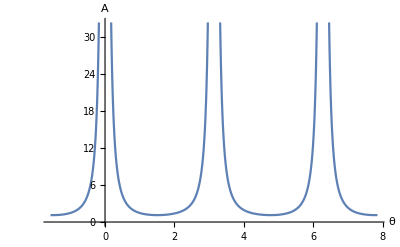

```mathematica
Plot[Aunit[traj, θ], {θ, -π/2, 5π/2},AxesLabel->{"θ","A"}]
```

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMC[ϕ_, ρ_]:=(2-ρ)/ρ+1/(2ρ ϕ^2)
```

Check This should be equal to Equation (1) for θ = π/2 and β=0:

```mathematica
FullSimplify[F[0,ϕ, π/2, ρ, r] == AHMC[ϕ, ρ]]
```

True

Showing the change in the HMC integrated autocorrelation varying with acceptance rate,

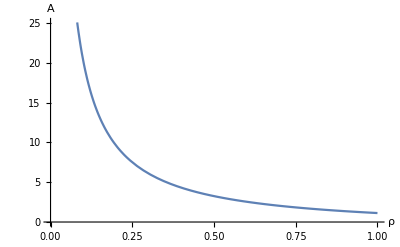

```mathematica
Plot[A[traj, π/2,ρ],{ρ, 0, 1},AxesLabel->{"ρ","A"}]
```

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMCunit[ϕ_] :=1+1/(2 ϕ^2)
```

Check This should be equal to Equation (1) for θ=π/2, β=0 and ρ=1:

```mathematica
FullSimplify[AHMCunit[ϕ]==F[0, ϕ, π/2, 1, r]]
```

True

## Inverse Laplace Transforms: Regular GHMC Autocorrelations

Inverting the autocorrelation functions gets very messy and so starting in reverse order now makes more sense, leaving the most complicated for last.

There is a sepcific method provided in the paper however, partial fraction decomposition is not well supported in Mathematica so it makes more sense to simply force the result for those that are not immediately obvious.

## HMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMCunit = InverseLaplaceTransform[FHMCunit[β ,ϕ, r],β,t] //ToRadicals;
```

```mathematica
CHMCunit[t_, ϕ_,r_ ] := Evaluate[iFHMCunit]
```

```mathematica
CHMCunitn[t_, ϕ_,r_ ] := CHMCunit[t, ϕ,r]/CHMCunit[0, ϕ,r ]
```

Plotting shows the underdamped form for unit mass and averge trajector length τ,

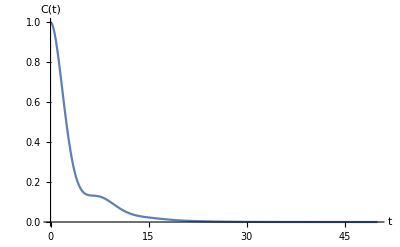

```mathematica
Plot[CHMCunitn[t, traj, rate], {t, 0, tf},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]
```

### HMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMC = InverseLaplaceTransform[FHMC[β ,ϕ,  ρ, r],β,t] //ToRadicals ;
```

```mathematica
CHMC[t_, ϕ_, ρ_, r_ ] := Evaluate[iFHMC];
CHMCn[t_, ϕ_, ρ_, r_ ] :=CHMC[t, ϕ, ρ, r]/CHMC[0, ϕ, ρ, r] ;
```

Plotting for varying acceptance rate at t=0,

```mathematica
Plot3D[CHMCn[t, traj, ρ,rate], {ρ, 0., 1.},{t, 0., tf}, PlotRange->{0,1},AxesLabel->{"ρ","t","C(0)"}]
```

-Graphics3D-

Plotting for non unit acceptance and a small mass,

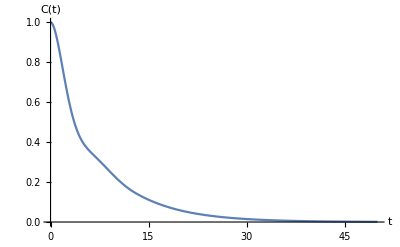

```mathematica
Plot[CHMCn[t, traj*0.4,0.65, rate], {t, 0, tf},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]
```

## GHMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFunit = InverseLaplaceTransform[Funit[β, ϕ, θ, r],β,t] //ToRadicals;
```

```mathematica
Cunit[t_, ϕ_, θ_, r_] := Evaluate[iFunit];
Cunitn[t_, ϕ_, θ_, r_] = Cunit[t, ϕ, θ, r]/Cunit[0, ϕ, θ, r];
```

checking against the HMC case,

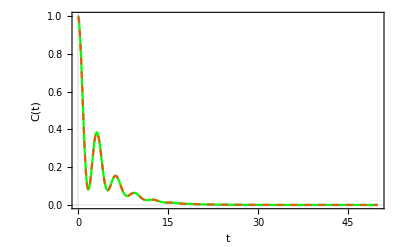

```mathematica
plot1 = Plot[Cunitn[t, traj, π/2,rate],{t,0,tf},
PlotTheme->"Scientific",PlotStyle->Green,PlotRange->{0,1},AxesLabel->{"t","C(t)"}];
plot2 =Plot[CHMCunitn[t,traj, rate], {t, 0, tf},
PlotTheme->"Scientific",PlotStyle->Dashed,PlotRange->{0,1},AxesLabel->{"t","C(t)"}];
Show[plot1,plot2]
```

### GHMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

#### Warning: Extremely large computation time!

This equation is huge and crashes Mathematica with even 8GB RAM and so the result is saved to a text file

The text file should not be opened manually as it will be about 20 MB and will also crash most text editors

Cleaning up the string with python code can reduce the total size to ~170 KB

A cleaned version can be found in theory/__CmainBody.txt

The text file is evaluated directly as python code by eval() in theory._mathematicaFunctions.expC()

```mathematica
(*iF = InverseLaplaceTransform[F[β, ϕ, θ,  ρ, r],β,t];
CF[t_, ϕ_, θ_,  ρ_, r_] := Evaluate[iF]*)
(*Export["equation.txt",ToString[CF[t, phi, theta, pa, r],FortranForm]];*)
```